# On Proportional Braking in H Bridges

Robert Atkinson
14 August 2018

Most H bridge designs use one of two common switching modalities, which are usually termed ‘lock anti-phase’ and ‘sign-magnitude’ respectively (Ref: http://www.modularcircuits.com/blog/articles/h-bridge-secrets). However, the STMicroelectronics VNH5050E H bridge, used in FTC motor controllers for nearly a  decade, employs neither of these modalities, instead using what can be called an ‘asynchronous sign-magnitude’ switching modality. In addition to it’s driving modes, as was observed by Eric & Douglas Chin, this modality admits a mode wherein dynamic-braking is applied in proportional to the PWM duty cycle, which we term ‘proportional braking’. Here, we explore why using proportional braking might be advantageous, and the details of doing so.

## Section. Introduction

### Section.Subsection. Administrivia

Before we begin, we load in some previously computed logic.

```mathematica
Get[NotebookDirectory[] <> "Utilities.m"]
inputDirectory = FileNameJoin[{NotebookDirectory[],"MotorPhysicsGearsInitialConditions.Output"}] <> $PathnameSeparator;
Get[inputDirectory <> "ParametersUnitsAndAssumptions.m"];
Get[inputDirectory <> "MotorModels.m"];
Get[inputDirectory <> "MotorTimeDomainFunctions.m"];
Get[inputDirectory <> "Misc.m"];
```

### Section.Subsection. H Bridge Architecture

In order to appreciate the design task explored in this document, it is important to have a comfortable, detailed working understanding of the operation of H bridges. From a simplified perspective, an H Bridge can abstractly be thought of as a circuit involving a motor, a voltage source, and four switches (Ref: https://en.wikipedia.org/wiki/H_bridge):

-Graphics-

In this document, we need to be able to discuss with some precision the state of these switches. As there are four switches, there are 16 possible states. We will number those states by assigning weights to each switch, and summing over the weights of the switches which are closed in any particular state. We assign weights as follows: S1 → 8,  S2 → 4,  S3 → 2,  and S4 → 1. With that nomenclature in hand, the motor’s response in each of the 16 states is as follows:

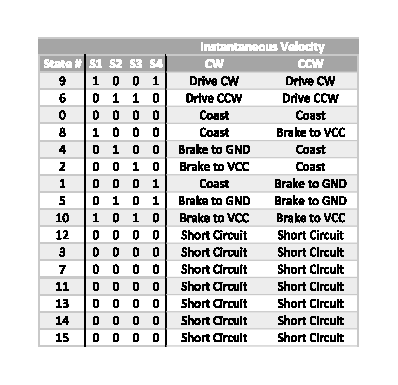

Note that in a design where an H bridge is driven by pulse width modulation, we can talk with precision about the operation of the bridge by naming the state used in the “on” part of the PWM cycle, the state used in the “off” part of the cycle, and the duty-cycle percentage of the “on” state as a fraction of the PWM framing period (which is contextually herein taken as fixed). Thus, for example, we might talk about an H bridge using a 6/2 mode being driven at a 75% duty cycle, or a bridge in 5/0 mode with a 30% duty cycle, etc.

States 9 and 6 are the driving states. In state 9, the motor turns one direction, which we have arbitrarily labeled as CW (or, more precisely, it attempts to increase its angular velocity in the CW direction). In state 6, the motor turns CCW. In state 0 it coasts, while in states 5 and 10 rheostatic dynamic braking is employed (Ref: https://en.wikipedia.org/wiki/Dynamic_braking), either through the ground rail or the power rail. Seven of the states are short circuits, and should be avoided.

States 8, 4, 2, and 1 deserve special mention. Their behavior is dependent not only on the state of the switches, but also on the sign of the instantaneous angular velocity.  This is due to consequences of the fact that a more complete picture of an H bridge must include the so-called ‘catch diodes’ whose presence is necessary to avoid inductive voltage spikes during switching transitions (Ref: http://modularcircuits.tantosonline.com/blog/articles/h-bridge-secrets/h-bridges-the-basics/).

-Graphics-

Let us consider state 8, where S1 (aka Q1) is closed, and the remaining switches are open. If we are driving CW, and, say, switching between state 9 and state 8 over a PWM frame (which we will denote as the 9/8 mode), then as switch S4 is opened, the inductive motor current briefly discharges across D1 (in FTC motors, ‘briefly’ is about 1ms). Because the shaft is turning CW, the polarity of the motor’s back EMF is such that it cannot drive current through that same route. All is well: we drive forward.

However, consider the case where we had been driving in the CCW direction, using, say, the 6/2 mode, so that the motor shaft is currently rotating CCW. Then, were we to switch to 9/8 mode, we find that the polarity of the motor’s back EMF is the other way around; it can now also drive current through the diode, and we find ourselves in a dynamic braking situation.

States 4, 2, and 1 have analogous behavior.

### Section.Subsection. Forward Driving vs Proportional Braking vs Reverse Driving

The STMicroelectronics VNH5050E H bridges used in FTC use 9/8 and 6/2 driving modes. Thus, the behaviors of states 8 & 2 mentioned above are pertinent.

Suppose we are driving CW, cruising along, forward driving using mode 9/8 (the 6/2 case is analogous), having developed some non-zero velocity in the shaft. Then, suppose further that our PID loop discerns that we’re going a little too fast. At first, it will ask us to take our foot off the gas a little, which we do by reducing the 9/8 duty cycle. But if after that we’re still going too fast, the PID loop will ask us to take stronger measures. What the current (August 2018) firmware does in response to that request is to start driving in the other direction (i.e. CCW, using mode 6/2). This we’ll call reverse driving (reverse in the sense that it’s opposite to the direction of the shaft rotation). Reverse driving brings in to play the ‘brake to VCC’ behavior of state 2.

The problem is that it’s impossible to decelerate gently drive using reverse driving. This is because even 6/2 reverse driving with only the minimum possible 0% duty cycle is effectively (except for a diode voltage drop) a fully dynamic braking situation; as we increase the duty cycle percentage, this braking is only augmented by additional motor torque actively driving backwards. The transition from 0% forward driving to 0% reverse driving is thus a very abrupt one.

With asynchronous sign-magnitude H bridges such as the VNH5050E there is a third mode we can avail ourselves of to help ease this transition: mode 5/0, which we call proportional braking. In state 5, S2 and S4 are closed, causing dynamic braking; in state 0, all switches are open. A 0% duty cycle proportional braking thus is a (zero-torque) open circuit where we coast, just we do in 0% 9/8 forward driving. At the other extreme, 100% proportional braking is full dynamic braking, just as 0% reverse driving is (again, ignoring the diode drop for the moment). In between, the balance of braking vs coasting is controlled by the PWM duty cycle. Thus, proportional braking provides a transitional regime between forward driving and reverse driving that we can exploit to respond smoothly to the PID loop’s request for increasing amounts of deceleration.

The design challenge is to select the points in the control signal coming from the PID loop where we transition from one regime to the other. There are four points of relevance, which are as follows.

S, the point of 100% reverse driving. It is is clear that this occurs at the negative extreme of the PID control signal range.

G, the point of 100% forward driving. This occurs at the positive extreme of the PID control signal range.

Z, the point of 0% proportional braking and 0% forward driving.

T, the point of 0% reverse driving and 100% proportional braking (we again ignore the diode for now).

A question arises as to the behavior of the driving regimes between these four points, where the PWM duty cycle is neither 0% nor 100%. As we presently lack any information to the contrary, we will in the below depict the regimes as linear in the duty cycle. This is certainly at least a roughly-good approximation at the time scale that is seen by the motor shaft, though it is only an approximation. Influences such as the ripple current LR time constant being several PWM cycles and thus never fully decaying might, for example, cause an offset bias in the linearity. Detailed investigation of the shape of these curves awaits future analysis.

As a general scheme, the four points S, T, Z, and G are structurally related relative to each in the order illustrated below.  Forward driving is shown in green, proportional braking in blue, and reverse driving in red.

```mathematica
Clear[abscissa, ordinate, line, points, pointNames, plotPoints]; 
abscissa[pt_] := pt[[1]]
ordinate[pt_] := pt[[2]]
line[{x1_, y1_}, {x2_, y2_}] := Function[{x}, y1 + (y2 - y1) / (x2 - x1) * (x - x1)]
points = { S -> {-controlMax, yReverse100},  T -> { controlProp100, yProp100 }, Z -> {controlProp0, yProp0}, G-> {controlMax, yForward100}};
pointNames = { S, T, Z, G };
Options[plotPoints] = { xOver -> 1.1, yOver -> 1.2 } ~Join~ Options[Plot] ~Join~ Options[ListPlot];
plotPoints[pointsN_, title_, yLabel_, opts: OptionsPattern[]] := plotPoints[pointsN, title, yLabel, 32767, opts];
plotPoints[pointsN_, title_, yLabel_, controlMax_, opts: OptionsPattern[]] := Module[
{zg, tz, st, yMax, clampMag, range,frame, listPlot,  reverse, braking, forward, plot},
zg = line[Z, G]/. pointsN;
tz = line[T, Z]/. pointsN;
st = line[S, T]/. pointsN;
yMax = Max[st[-controlMax] // Abs, zg[controlMax] // Abs];
clampMag[control_] := Max[Min[control, controlMax], -controlMax];
range[x_, p1_, p2_] := {x, (p1 /. pointsN)[[1]], (p2 /. pointsN)[[1]]};
frame = ListPlot[{{-controlMax*OptionValue[xOver], -yMax}, {controlMax * OptionValue[xOver], yMax}}, PlotStyle-> PointSize[0],
PlotRange-> {-yMax * OptionValue[yOver], yMax * OptionValue[yOver]},
 AxesLabel->{"control", yLabel}, 
PlotLabel->title, 
FilterRules[{opts}, Options[ListPlot]]// Evaluate
];
listPlot = ListPlot[{ S -> "S", T -> "T", Z -> "Z", G-> "G"} /. pointsN, 
PlotStyle->Black, 
FilterRules[{opts}, Options[ListPlot]]// Evaluate];
plot[p1_,p2_, style_] := Plot[Evaluate[line[p1, p2] /. pointsN][x], Evaluate[range[x, p1, p2]], 
PlotStyle->style, 
FilterRules[{opts}, Options[Plot]] // Evaluate];
reverse = plot[S, T, Red];
braking = plot[T, Z, Blue];
forward = plot[Z, G, Darker[Green]];
Show[frame, listPlot, reverse, braking, forward]
]
```

```mathematica
examplePoints = {S -> {-32767, -100}, T -> {-16384, -70}, Z -> {8192, 30}, G -> {32767, 92}}
plotPoints[examplePoints, "Relative Structure of Points", "y"]
```

#### Section.Subsection.Subsubsection. Interpreting S, T, Z, and G

Our job here in this present document is to figure out how to locate the coordinates of the four points S, T, Z, and G for real driving situations based on sound, cogent principles.

Each time we run the PID control loop (currently every 50ms), we will calculate the coordinates of each of the four points according to the set of principles we have chosen. From those coordinates, the driving regime (forward, braking, reverse) is determined according to the position of the PID output control signal relative to the abscissas of the four points. The PWM duty cycle is then determined by the fractional location of the PID output control signal within the regime so located. The H bridge operating mode corresponding to the driving regime and the calculated duty cycle are then passed to the H bridge.

For example, suppose that during a PID loop run, the four points happen to be as in the above figure, and that the control output from the PID loop is currently -10000. Then, because abscissa[T] < -10000 < abscissa[Z], we will use proportional braking, and the duty cycle used will be 74%:

```mathematica
(pidOutput-(Z/.examplePoints//abscissa))  /  ((T/.examplePoints//abscissa)-(Z/.examplePoints//abscissa)) /. 
pidOutput->-10000 // N
```

### Section.Subsection. Roadmap

In what follows, the location of the abscissas of S & G and either Z or T in the PID control range will be determined a priori based on external considerations, and the location of the remaining point then determined from the other three using arguments of linearity. We will examine three different schemes, Scheme A, Scheme B, and Scheme C.

## Section. Scheme A

### Section.Subsection. Introduction: Points S, T, and G

The signature characteristic of the first scheme we examine is that it attempts to map in a linear manner the control signal coming from the PID loop to an “instantaneous equivalent applied DC voltage”. That is, for any H bridge switching mode and duty cycle, this scheme attempts to determine the applied voltage that would produce the same motor response in a dual system that lacked the H bridge but instead had a DC voltage source directly connected to the motor.

For some switching modes and duty cycle combinations, this equivalence is clear.

At G (100% forward driving; e.g. 100% state 9), the motor is connected between battery and ground 100% of the time. The equivalent applied voltage is thus clearly the battery voltage.

Similarly, at S (100% reverse driving), the equivalent applied voltage is the negative battery voltage

At T (100% proportional braking, ie: 100% state 5), the motor leads are shorted together; the equivalent applied voltage is thus zero volts. The same is also true (ignoring the diode) for 0% reverse driving (e.g.: 100% state 2). Further, given the equivalent voltages of G and S just discussed, if the overall scheme is to map the control signal to equivalent voltage linearly, then it follows that T must have a control value of zero.

With these in hand, and recognizing that Z must lie between T and G, we can visualize Scheme A as having the following overall shape. The particular value of Z shown is for illustrative purposes only.

```mathematica
Clear[plotScheme]; 
schemeA = {controlProp100 -> 0, yProp100 -> 0, yReverse100 -> -yMax, yForward100 -> yMax};
schemeAExample = schemeA ~Join~ {controlProp0 -> 2controlMax /3, yProp0 -> 2 yMax / 3};
plotScheme[scheme_, title_, yAxis_, yMaxVal_] := Module[
{scale = {controlMax -> 32767, yMax -> yMaxVal}, pointsN},
pointsN = points //. scheme /. scale;
plotPoints[pointsN, title, yAxis]
]
plotScheme[schemeAExample, "Scheme A", "Instantaneous Equivalent Applied DC Volts", 12]
```

### Section.Subsection. Point Z

The situation at Z is a bit tricker. Here (0% proportional braking/100% state 0, and 0% forward driving, 100% state 8) we have an open circuit, either literally, or nearly so (because of the diode). How can we map this open circuit into a closed circuit equivalence with some applied voltage?

The approach we examine is to recognize that in an open circuit, the current is zero (and thus the torque is zero as well, but we’ll focus on current). We then ask ourselves, given the instantaneous state of the system (ie: some instantaneous velocity Ω), in the H-bridgeless-dual is there a DC voltage we could apply that would yield zero current? The answer is, messily, “sort of”.

#### Section.Subsection.Subsubsection. vg(t)==vapp(t) as an approximation to the “zero current voltage”

Recall (see https://github.com/rgatkinson/RobotPhysics/blob/master/MotorPhysicsGearsInitialConditions.pdf) the differential equation in our model that links applied DC voltage vapp(t), the back EMF voltage vg(t), and the current i(t) is the following:

```mathematica
(voltageEqn = diffEqns[[3]]) // prettyPrint
```

An approximate argument goes something like this. If the current is zero, then the second term on the left disappears. Further, while initially there’s a transient, the current soon stabilizes, and thus the first term will also disappear. That leaves us with the following:

```mathematica
voltageEqn /. {i[t] -> 0, i'[t] -> 0} // prettyPrint
```

That is, if the applied voltage matches the generated EMF, there should be no current. However intuitive that equivalence might be (or not), it is is clearly only an approximation, for (at least) two reasons:

The current isn’t instantaneously zero, but instead must adjust through a transient

After the voltage is dropped from the voltage that produced steady state velocity Ω to that of the back EMF, the velocity necessarily declines, which produces less back EMF. Thus, whatever voltage balance there was to achieve zero necessarily degrades.

The important question, then, is “how good of an approximation is it?” Let us examine that in some detail.

#### Section.Subsection.Subsubsection. Analyzing vg(t)==vapp(t)

It turns out that in the modelling work referenced above, we have a complete, closed form, analytic result for the current as a function of time in a motor with gearbox as the voltage steps at time zero from steady state applied voltage vapp0 to some subsequent applied voltage vapp0 + ΔvappConst. This result is also parameterized on the motor model parameters (R, L, etc), the motor load after the gearbox(if any), and an optional externally applied torque (if any). We illustrate that result here in its entirety in order that the reader may have some understanding of its complexity and completeness; however, in future we will refrain from directly illustrating such complex functions, as they are very difficult to appreciate in detail.

```mathematica
curStepGeneric
```

If we forget about the externally-applied torque, the result does become simpler, but is still significantly complex:

```mathematica
curStepGenericNoExternalTorque = curStepGeneric /. { τapp0 -> 0, ΔτappConst->0}//FullSimplify // Expand // FullSimplify
```

Because of this complexity, in order to explore the effect on current of the drop of applied voltage to the back EMF we choose (initially, at least) to do so in the context of a concrete motor and particular loads. Here, we use an Andy Mark NeveRest 60 motor with either a 10kg or a 1kg flywheel attached:

```mathematica
aMotor = motorParameters["AM 60 A"];
aFlywheel = flywheel[Quantity[10, "kg"], Quantity[10,"cm"]] // siUnits;
aMotorWithFlywheel = addMotorLoad[aMotor, aFlywheel] // siUnits;
unitlessMotorWithFlywheel = aMotorWithFlywheel // siUnits // clearUnits;
aMotorWithFlywheel
```

We want to explore the current as a function of the steady state pre-gearbox velocity Ω. To do that, we first construct a function that gives us the applied voltage that must be in effect to achieve the steady state velocity Ω.

```mathematica
vappFromVelocity[Ω_, motor_] := Module[{eqn}, 
eqn = (θ'[ss0] /. (initialConditions /. Equal -> Rule)/. τapp0 -> 0 /. motor) == Ω;
vapp0 /.(uniqueSolve[eqn, vapp0]// First)]
vappFromVelocity[Ω, unitlessMotorWithFlywheel]
```

We also construct a function that gives us the back EMF as a function of Ω.

```mathematica
vgFromVelocity[Ω_, motor_] := Module[{v1, eqn}, 
v1 = vappFromVelocity[Ω, motor];
(vg[ss0] /. (initialConditions /. Equal -> Rule)/. τapp0 -> 0 /. motor)/. vapp0 -> v1]
vgFromVelocity[Ω, unitlessMotorWithFlywheel]
```

This should, of course, come out as Ke Ω, and, gladly, it does (remembering we’re dealing here with pre-gearbox Ke and Ω). With these in hand, we can define a function that pairs up the two voltages in question as an input to our general current result.

```mathematica
dropToVg[Ω_, motor_] := Module[{v1 = vappFromVelocity[Ω, motor], v2 =  vgFromVelocity[Ω, motor]},
Association[vapp0->v1, ΔvappConst -> v2 - v1]
]
dropToVg[2, unitlessMotorWithFlywheel]
```

Let’s put that all together, illustrating the result for some reasonable initial velocity. The maximum velocity of the motor and load example we’ve been working with is about 610.4 radians / second (before the 60:1 gearbox) when on a 12 volt battery:

```mathematica
ssSimple = ss /. {vapp0->0, τapp0 -> 0, ΔτappConst -> 0};
maxVelExample = ssVel /. ssSimple /. unitlessMotorWithFlywheel /. ΔvappConst -> 12 // N
```

We arbitrarily plot at 10% of the maximum velocity, and for 50ms, as that is the PID update interval in the FTC expansion hub firmware.

```mathematica
Clear[fn]
fn[Ω_] := curStepGenericNoExternalTorque /. unitlessMotorWithFlywheel /. dropToVg[Ω, unitlessMotorWithFlywheel] // N // FullSimplify
Plot[fn[maxVelExample/10], {t, 0, .050}, AxesLabel->{"Seconds", HoldForm[Amps]}, PlotRange->All, AxesOrigin->{0,0}]
Plot[fn[maxVelExample/10], {t, 0, .050}, AxesLabel->{"Seconds", HoldForm[Amps]}, PlotRange->{0, 0.005}, AxesOrigin->{0,0}]
```

(Note: the shape of these plots is characteristic; the vertical axis scales linearly with initial velocity:)

```mathematica
fn[n Ω]/fn[Ω] // FullSimplify
```

It is worthy of note that the current never does, in fact, reach zero. Further, over the course of the PID update interval, the current is distinctly non-zero throughout, by the end recovering maybe some ~20% of its initial value. The approximation here to a “zero current voltage” does not appear to be a very good one.

#### Section.Subsection.Subsubsection. “Mean zero current” as an approximation to the “zero current voltage”

The above analysis does suggest a different approximation: instead of dropping from the steady state applied voltage to the voltage of the back emf, to what voltage would we have to drop in order to have the mean (i.e: average) current over the PID interval be zero? We compute that here as a function of the steady state velocity Ω.

```mathematica
vappFromVelocity[Ω, {}]
currentFromΩAndDrop = curStepGenericNoExternalTorque /. vapp0 -> vappFromVelocity[Ω, {}] // FullSimplify
```

The value ΔvappConst in the above is the voltage drop we seek. We next symbolically compute the mean current over the PID interval.

```mathematica
meanCurrent = Integrate[currentFromΩAndDrop, {t, 0, pidPeriod}] /pidPeriod
```

We set that equal to zero, and solve for the voltage drop.

```mathematica
ΔvappMeanZeroCurrent = ΔvappConst /. uniqueSolve[meanCurrent==0, ΔvappConst] // FullSimplify // Expand // FullSimplify
```

This is, ehem, a mouthful. In particular (among many things), it is sensitive to the load on the motor (Jafter, Bafter), which would significantly complicate its application in the FTC context (teams would need to measure their robots). Nevertheless, let’s see this in action for the same example motor and load we looked at previously.

```mathematica
dropToMeanZeroCurrent[ΩΩ_, motor_] := Module[{
v1 = vappFromVelocity[ΩΩ, motor], 
Δv2 = ΔvappMeanZeroCurrent /. motor /. pidPeriod -> .050 /. Ω -> ΩΩ},
Association[vapp0->v1, τapp0 -> 0, ΔvappConst -> Δv2]
]
dropToMeanZeroCurrent[1, unitlessMotorWithFlywheel] // N
```

```mathematica
Clear[fn]
fn[Ω_] := curStepGenericNoExternalTorque /. unitlessMotorWithFlywheel /. dropToMeanZeroCurrent[Ω, unitlessMotorWithFlywheel] // N // FullSimplify
Plot[fn[maxVelExample/10], {t, 0, .050}, AxesLabel->{"Seconds", HoldForm[Amps]}, PlotRange->All, AxesOrigin->{0,0}]
```

At first glance, it would indeed seem to be plausible that we’ve done the math correctly, i.e., that the mean current over the PID interval is zero (that’s just a sanity check: assuming we’ve set the equations up correctly, the solution must be correct, assuming Mathematica has not encountered a bug). Further, comparing this approximation of the zero current voltage to the previous vg(t)==vapp(t) approximation, it is hard to argue that the mean zero current approximation is not both numerically and conceptually superior.

However, as was noted, its operational difficulties make its deployment a challenge. While perhaps some simplification of this result (e.g., perhaps ignoring the load?) might produce an approximation of intermediate goodness that was deployable, such an investigation has not yet been carried out. Accordingly, for the remainder of the discussion of Scheme A, we will work with the vg(t)==vapp(t) approximation for the zero current voltage.

### Section.Subsection. Calculating Point Z

Recall the structure of Scheme A:

```mathematica
plotScheme[schemeAExample, "Scheme A", "Instantaneous Equivalent Applied DC Volts", 12]
```

We have points S, T, and G in hand; we wish to compute point Z. The principle we will use is to locate Z on the line between T and G. Per the above, we take the ordinate of Z to be the current instantaneous back EMF; our job is to compute the abscissa of Z, which we will denote as controlProp0 (0% proportional braking occurs at the same location as 0% forward driving). The calculation is pretty straightforward.

```mathematica
schemeA = Union[schemeA, {yProp0 -> vgFromVelocity[Ω, {}]}]
```

```mathematica
schemeAPoints = points /. schemeA /. yMax -> batteryVoltage
```

```mathematica
schemeAEqn =((line[T, G] /. schemeAPoints)[controlProp0] == (yProp0 /. schemeA))
```

```mathematica
schemeASoln = uniqueSolve[schemeAEqn, controlProp0]
schemeAResult =  schemeAPoints/. schemeASoln
```

Recall from the modelling paper that Ke is the before-gearbox electrical coupling constant. Thus, the abscissa of Z is a multiplication of the motor velocity (in radians / second) by a motor constant and the control range magnitude and a division by the battery voltage.

Let’s explore a little how the location of Z varies with velocity Ω. We plot Z at various fractions of the maximum velocity (10%, 50%, and 90%):

```mathematica
plotSchemePointsExample[schemeResult_, titlefn_, yLabel_] := Module[{ptsFromVel, plotVel},
ptsFromVel[ΩΩ_] := schemeResult /. 
{controlMax -> 32767, batteryVoltage->12} /. unitlessMotorWithFlywheel /. Ω->ΩΩ;
plotVel[Ω_] := Module[{title = titlefn[Ω]},
plotPoints[ptsFromVel[Ω], title, yLabel, ImageSize->300, yOver-> 1.2]];
plotVel[maxVelExample * #]& /@ {0.1, 0.5, 0.9} // Row
]
plotSchemePointsExample[schemeAResult, "Scheme A Example, Ω=" <> ToString[#] <> " rad/s"&, "Volts"]
```

It is significant to note that as velocity increases, the amount of the control range allocated to the forward driving regime diminishes, ultimately to zero. In many (if not most) FTC motor control situations, the control loop spends the majority of its time in the forward driving regime. There seems to be a tension between these situations.

## Section. Scheme B

### Section.Subsection. Introduction

We now discuss a second scheme, Scheme B. This scheme is motivated by a few observations.

In actual practice, the PID loop visits point Z far more often than it visits point T (or S). Thus, to help achieve reproducible results when driving, it is preferable to have any uncertainty or variability in the calculation of the locations of the points to be attributed to point T rather than point Z. That is, all other things being equal, it is preferable to have point Z determined a priori, and point T calculated at runtime.

As was discussed at some length above, the calculation of a equivalent applied DC voltage that produces instantaneous zero current is an elusive proposition. Moreover the only feasibly-calculable approximation thereto that we have is demonstrably poor.

In practice in FTC situations, the PID algorithm spends the majority of its time in the forward driving regime. Thus, attenuation of the dynamic range of that regime is of concern so as to avoid precision loss in calculations.

The point Z is by its definition a point of zero current. It thus makes sense to at least explore an instantaneous-current-linearization (in contrast to the instantaneous-equivalent-applied-voltage-linearization previously examined).

Scheme B is the exploration of such an instantaneous-current-linearization. From these observations, we can deduce a few facts.

The point Z is at the origin: it’s ordinate is zero, because the y axis is torque; it’s abscissa is zero because no other fixed abscissa is reasonable.

The point G has an abscissa of controlMax, but it’s ordinate will be a function of the battery voltage, the back EMF, and the motor resistance.

Similarly, point S has an abscissa of -controlMax, and an ordinate which is a function of the battery voltage, the back EMF, and motor resistance.

The ordinate of point T is a function of the battery voltage, the back EMF, and motor resistance; its abscissa will be an interpolation between Z and S.

The general structure of Scheme B looks something like this:

```mathematica
schemeB = {controlProp0 -> 0, yProp0 -> 0, yReverse100 -> - yMax, yForward100 -> yMax /2};
schemeBExample = schemeB  ~Join~ {controlProp100 -> -controlMax /2, yProp100 -> -yMax /2}
plotScheme[schemeBExample, "Scheme B Example", "Current (Amps)", 3]
```

Lets explore this in more detail.

### Section.Subsection. Current as Function of State

We calculate the current in instantaneous steady state (i.e. after the LR transient) as a function of the applied voltage and instantaneous current velocity. Note that as was the case in Schema A, this is only an approximation.

```mathematica
ssCurrentFromVoltageVelocity[v_, Ω_] := Module[{eqn, soln},
eqn = voltageEqn /. { vg[t] -> vgFromVelocity[Ω, {}], vapp[t] -> v, i'[t] -> 0};
soln = uniqueSolve[eqn, i[t]] // FullSimplify;
i[t] /. soln
]
ssCurrentFromVoltageVelocity[v, Ω]
```

### Section.Subsection. Locating Our Points

With that in hand, we can determine the ordinates of S and G from the relationship of current to the battery voltage and velocity; the ordinate of T is calculated similarly, but with respect to the zero applied volts of 100% state 5. Point Z is at the origin, as was mentioned.

```mathematica
schemeB = {
yForward100 -> ssCurrentFromVoltageVelocity[batteryVoltage, Ω],
yReverse100 -> ssCurrentFromVoltageVelocity[-batteryVoltage, Ω],
yProp100 -> ssCurrentFromVoltageVelocity[0, Ω],
controlProp0->0, yProp0->0
}
```

With that we can calculate the abscissa of T by fixing T on a line from S to Z.

```mathematica
schemeBPoints = points /. schemeB
```

```mathematica
schemeBEqn =((line[S, Z] /. schemeBPoints)[controlProp100] == (yProp100 /. schemeB))
schemeBSoln = uniqueSolve[schemeBEqn, controlProp100]
schemeBResult = schemeBPoints/. schemeBSoln
```

Note that this result is only dependent on the instantaneous velocity and battery voltage, the control range, and the motor’s pre-gearbox electrical coupling constant: conveniently, the uses of the motor’s resistive constant R values have all cancelled out.

### Section.Subsection. Examples

As we did with Scheme A, we illustrate Scheme B with our working motor example at a few different velocities.

```mathematica
plotSchemePointsExample[schemeBResult, "Scheme B Example, Ω=" <> ToString[#] <> " rad/s"&, "Current (Amps)"]
```

These examples clearly illustrate the most significant tradeoff involved in the use of Scheme B: that we get a knee at the origin (note that we are still continuous everywhere). While the knee is relatively shallow at low velocities, it is more pronounced at larger ones This is not intrinsically a problem: architecturally speaking, a PID loop can certainly deal with such a condition; while all other things being equal, we’d prefer not to have the knee, the reality is that all other things are not equal, as was discussed at the beginning of this section. From one point of view, this knee is the price we pay for moving the uncertainty and variability of the abscissa of Z that is present in Schema A to an uncertainty and variability of the abscissa of T in Scheme B. Further, the dynamic control range allocated to forward driving remains large, and insensitive to velocity.

These tradeoffs seem worthwhile.

## Section. Scheme C

In the introduction we stated the following:

“S, the point of 100% reverse driving. It is is clear that this occurs at the negative extreme of the PID control signal range.

G, the point of 100% forward driving. This occurs at the positive extreme of the PID control signal range.”

However, upon further reflection, we can see that these unconditional statements about the position of S and G in the control range can in fact be relaxed. In particular, we ought to ask ourselves the question “is it necessary or worthwhile to always provide the PID loop with access to the full range of the reverse driving regime?” For example, if we are in Scheme B with some significant velocity, proportional braking is strong, and so maybe we don’t need to map the upper end of reverse driving into the range [-controlMax, controlMax] as we have been doing so far. Scheme C explores that possibility.

Recall our result from Scheme B.

```mathematica
schemeBResult
```

In Scheme C, we stretch out the points S & T left of the Y axis so that they have the same slope as that of the line from Z to G.

```mathematica
computeSchemeC[points_] := Module[{scale, scalePt},
scale = -(S /. points)[[2]] / (G /. points)[[2]];
scalePt[pt_] := {pt[[1]] * scale, pt[[2]]};
{
S -> (S /. points // scalePt) , 
T -> (T /. points  // scalePt), 
Z-> (Z /. points),
G -> (G /. points)} // FullSimplify
];
schemeCResult = computeSchemeC[schemeBResult]
```

This produces a linear interpretation of the control signal across the entire control signal range. However, unlike Scheme B, for higher velocities, we rely much more on proportional braking that we do on reverse driving. Which seems to make sense, since at higher velocities proportional braking has more effect than it does at lower velocities.

```mathematica
plotSchemePointsExample[schemeCResult, "Scheme C Example, Ω=" <> ToString[#] <> " rad/s"&, "Current (Amps)"]
```

## Section. To Do

In Scheme B, calculate controlReverse0, dealing with the voltage drop across the catch diode. This doesn’t effect the above results, but will slightly alter the rescaling of control signal to duty cycle when in the reverse driving regime.

Can we improve on the approximation currently found in ssCurrentFromVoltageVelocity[]?

Consider presenting a ‘current plot’ of Scheme A to facilitate comparison between the schemes.

## Section. Revision History

2018.08.07 Initial version.

2018.08.13. Significant rewrite.

2018.08.14. Fix errors caused by switch from post-gearbox to pre-gearbox Ω. Minor prose corrections. Added Scheme C.